# Retrospective Analysis of the First Year of the COVID-19 Pandemic in the United States

The COVID-19 pandemic has been a transformative event that has challenged our assumptions about the world and our place in it. It is clear that the pandemic has had a profound impact on our lives, our communities, and our societies. Through careful analysis of the data and a commitment to evidence-based decision-making, we can learn from this experience and emerge stronger and more resilient as a society. Particularly the first pandemic year, in which countries and subregions across the globe saw themselves forced to act quickly as coordination would have involved lengthy discussion processes, offers the chance evaluate approaches and risks faced by individual administrative entities. This report uses Wolfram Research data [1] for an analysis based on the first year of the COVID-19 pandemic starting from the beginning of 2020.

```mathematica
pandemicData = ResourceData["Epidemic Data for Novel Coronavirus COVID-19", "WorldCountries"];
```

The G7 countries, which include the United States, Canada, Japan, Germany, France, Italy, and the United Kingdom, are among the most powerful and influential nations in the world. As such, they have a significant impact on global politics, economics, and social issues, including the COVID-19 pandemic. These countries have also been among the hardest-hit by the pandemic, with five of them being among the top nine regarding numbers of confirmed cases. Let’s display this in a way that clarifies the dimensions of the case numbers for those countries that have reached the 10 highest counts at the end of the observation period in the downloaded data (January 30th, 2022).

```mathematica
pandemicTop10 = pandemicData[TakeLargestBy[#ConfirmedCases["LastValue"] &, 10]][All, {"Country", "ConfirmedCases"}];
pandemicTop10 = MapAt[#["LastValue"]&, pandemicTop10, {All, "ConfirmedCases"}];
Show[SectorChart[Transpose[{ConstantArray[1, 10],Normal[pandemicTop10[All, "ConfirmedCases"]]}],ChartLegends->Normal[pandemicTop10[All, "Country"]], ChartStyle->ColorData[10, "ColorList"], LabelingFunction->(Callout[Row[{#[[2]]}], Automatic]&)], ImageSize->500,ImagePadding->10]
```

-Graphics-

As displayed, the United States were hit notably worse than other G7 countries, followed by France with less than half absolute confirmed cases compared to the US. Given their importance and the severity of the impact of the pandemic, it is crucial to examine how COVID-19 cases have developed in these countries and to identify patterns and trends that can inform policy decisions and improve preparedness for future public health crises. Since the United States has a particularly high case count, this analysis will focus on US pandemic data.

### The US and Other G7 Countries in the First Pandemic Year

Let’s look at incremental case numbers for all G7 countries, beginning in January 2020, when the first COVID-19 cases were confirmed in the US [2], through the first anniversary of the declaration of COVID-19 as a global pandemic by the WHO in March 2021 [2]. 
First, we narrow down our data to that of the G7 countries in the specified time frame.

```mathematica
pandemicCountryData = pandemicData // Select[(#Country == Entity["Country", "UnitedStates"]) || (#Country == Entity["Country", "Germany"] ) || (#Country == Entity["Country", "France"]) || (#Country == Entity["Country", "Italy"]) || (#Country == Entity["Country", "Canada"])|| (#Country == Entity["Country", "Japan"])|| (#Country == Entity["Country", "UnitedKingdom"])&] // #[All, {"Country", "ConfirmedCases"}]&;
pandemicCountryData = MapAt[TimeSeriesWindow[DeleteMissing[#], {{2020, 1, 20},{2021, 03, 11}}]& ,pandemicCountryData, {All, "ConfirmedCases"}];
```

To gain a better idea of how new case numbers rise and fell, we transform case data from cumulative to incremental by calculating the differences between cumulative counts.

```mathematica
pandemicCountryData = MapAt[Differences ,pandemicCountryData, {All, "ConfirmedCases"}];
```

For normalisation purposes, we add population counts and express case numbers as relative counts per 100,000 people.

```mathematica
pandemicCountryData= pandemicCountryData[All,Append[#,"Population"->#Country["Population"]]&];
norm[row_] := QuantityMagnitude[Divide[row["ConfirmedCases"],row["Population"]]]*100000
normedColumn = pandemicCountryData[All,norm] // Normal;
pandemicCountryData = Transpose[Append[Transpose[pandemicCountryData],"Norm"->normedColumn]];
```

In order to smooth out daily variability, we apply a mean filter to the incremental case data. This replaces each data point by the mean of its 604,800 - neighbourhood. In this case, since time stamps are interpreted in absolute time, this corresponds to producing the mean value of a two-week-long time period for each point in time.

```mathematica
pandemicCountryData =MapAt[MeanFilter[#, 604800]&,pandemicCountryData, {All, "Norm"}];
```

Finally, we plot this normalised, smoothed, incremental data for all G7 countries.

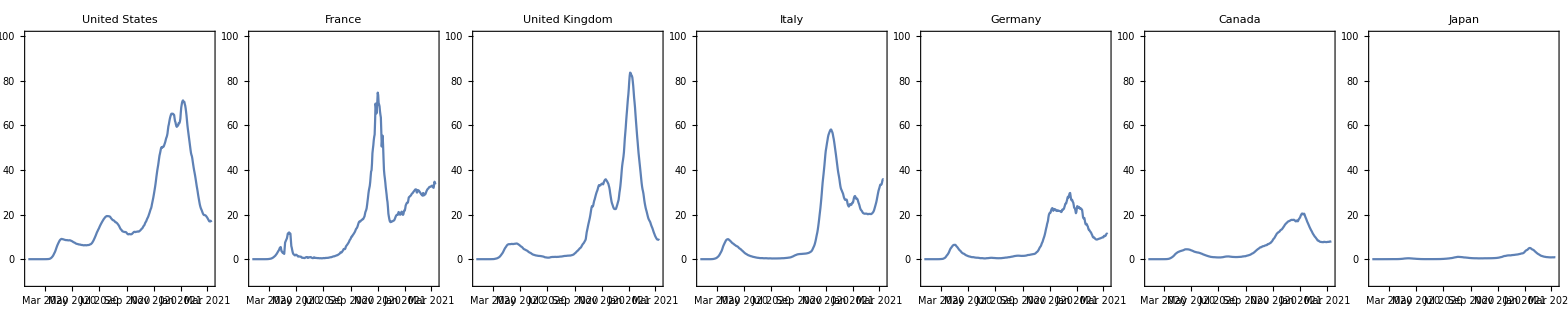

```mathematica
countryPlots = MapAt[DateListPlot[#["Norm"],PlotLabel -> Normal[#["Country"]["Name"]],  PlotRange -> {All, {-10, 100}}]&,pandemicCountryData,{All}];
Grid[{(countryPlots // Normal)}, Frame -> All]
```

This displays the trend of COVID-19 case data. Strikingly, Japan shows very small increases in case numbers over the whole time frame. For all other G7 countries, we can see a small increase in cases signifying the first wave in spring 2020. Beginning in October 2020, case numbers grew quicker and quicker due to the occurrence of at least one winter wave of COVID-19. Here, the normalized counts for the US follow a course similar to those of France or the United Kingdom, regarding timing as well as magnitude.
However, one has to keep in mind that despite the fact of the much greater population size of the US, the population density is much smaller than for France or the UK:

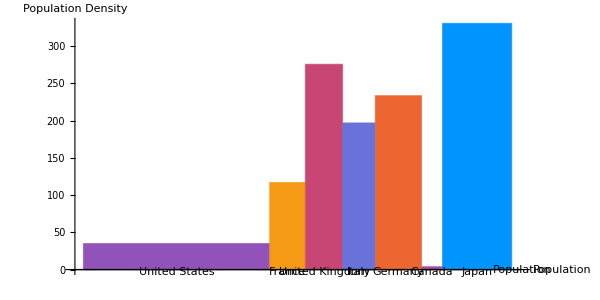

```mathematica
withArea = pandemicCountryData[All,Append[#,"Area"->#Country["Area"]]&];
popDensity[row_] := QuantityMagnitude[Divide[row["Population"],row["Area"]]];
densityColumn = withArea[All,popDensity] // Normal;
withArea = Transpose[Append[Transpose[withArea],"PopulationDensity"->densityColumn]];
RectangleChart[Transpose[{(QuantityMagnitude /@ Normal[withArea[All, "Population"]]),Normal[withArea[All, "PopulationDensity"]]}], ChartLabels->Normal[withArea[All, "Country"]], ChartStyle->ColorData[111], AxesLabel->{"Population", "Population Density"}, AspectRatio->0.5, ImageSize->600]
```

Here, we combined population data with area data for each G7 country to calculate population densities. The chart visualizes the fact that the US has a comparatively low population density for having the highest absolute population value. COVID-19 is spread through droplets containing the virus and thus caught more easily in crowded spaces [3]. Therefore, the US showing normalised case numbers similar to those of countries with a much more dense population highlights the importance of analysing US data to gather valuable insights that can inform future pandemic preparedness planning.

### The Third Wave in the US during the 2020/2021 Winter

Upon examining the trend of COVID-19 cases in G7 countries throughout the first year of the pandemic, an irregularity becomes apparent: while the significant rise in cases during the 2020/2021 winter corresponds to the second wave for all other countries, it constitutes the third wave for the United States, as the US seems to have experienced a summer surge. Before exploring this summer surge further, we will attempt to model the preliminary phase of the pandemic in the US prior to the onset of the winter surge, with the aim of investigating whether the summer wave could have been utilized to predict the occurrence and severity of the subsequent winter surge.

```mathematica
pandemicDataUS = ResourceData["Epidemic Data for Novel Coronavirus COVID-19", "WorldCountries"] // Select[#Country == Entity["Country", "UnitedStates"]&];
```

The data selected for modeling covers the time period from Mid March 2020, when the WHO declared COVID-19 a pandemic, until Mid October, right before cases started to rise, signifying the beginning of the winter surge.

```mathematica
dataTS = pandemicDataUS[[1]][["ConfirmedCases"]]// Differences // TimeSeriesWindow[#, {{2020, 3, 11},{2020, 09, 10 }}]&
```

TimeSeries[…]

As in the above, we express absolute incremental case numbers as relative counts per 100,000 people.

```mathematica
relativeCounts = Divide[#*100000, Entity["Country", "UnitedStates"]["Population"]]&;
dataTS = dataTS // TimeSeriesMap[relativeCounts, #]& // TimeSeriesMap[QuantityMagnitude, #]&
```

TimeSeries[…]

This is data that we can now model. We fit a nonlinear model that attempts to capture both COVID-19 waves as well as variability. The aim is to transform the time series such that we can fit a time series model to a stationary series, which we can then use to make forecasts.

FittedModel[3.08605+0.0793264 x+Cos[0.994899 x]+4.53526 Sin[5+0.07 x]]

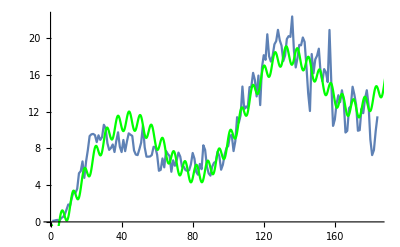

```mathematica
data = dataTS["Values"];
nlm = NonlinearModelFit[data, { Cos[g*x]+ c*Sin[0.07*x +5]+ x/d + e },{c, d, e, g}, x]
Show[ListLinePlot[data],Plot[nlm[x], {x, 0, 200}, PlotStyle->Green]]
```

Let’s look at the residuals in order to estimate if there are no patterns or trends left to explain.

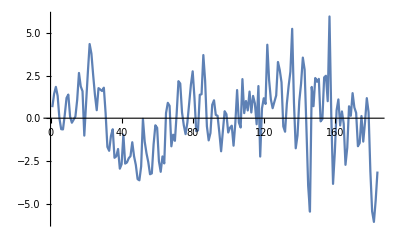

```mathematica
ListLinePlot[residuals]
```

The residuals appear to be centered around a mean of zero. In order to test the normality of the residuals, we first obtain the estimated parameters of a Gaussian distribution that best fits the data. Then, we conduct a hypothesis test to determine if the residuals were sampled from a Gaussian distribution with the estimated parameters.

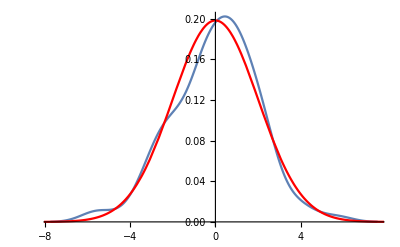

0.686687

```mathematica
residuals = nlm["FitResiduals"];
normDist = FindDistributionParameters[residuals, NormalDistribution[nu,sigma]];
Show[SmoothHistogram[residuals], Plot[PDF[NormalDistribution[normDist[[1, 2]],normDist[[2, 2]]],x], {x, -10, 10}, PlotStyle->Red]]
DistributionFitTest[residuals, NormalDistribution[normDist[[1, 2]],normDist[[2, 2]]]]
```

The residuals appear to be normally distributed, that means that we have successfully captured most of the variability in the data. We now have to check if they are uncorrelated as well.

| Estimate | Standard Error | t-Statistic | P-Value
1 | -0.0148167 | 0.112976 | -0.131149 | 0.895803
x | 0.661403 | 0.0563794 | 11.7313 | 5.30953×10^-24

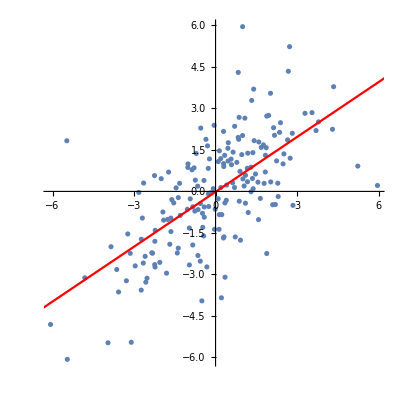

```mathematica
blurb = LinearModelFit[Partition[residuals, 2, 1], {1, x}, x];
blurb["ParameterTable"]
Show[ListPlot[Partition[residuals, 2, 1], AspectRatio-> 1],Plot[blurb[x],{x,-Length[residuals],2*Length[residuals]}, PlotStyle->Red]]
```

Apparently, the residuals are still correlated enough, such that there is a positive linear trend (with a statistically significant slope) between consecutive values. 
Let’s investigate the correlation function with its corresponding 90% confidence bands, based on 800 randomly shuffled surrogates.

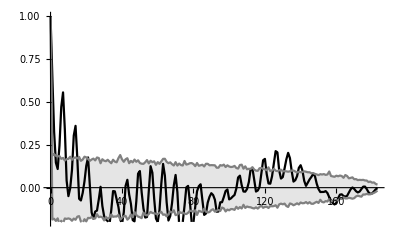

```mathematica
nVal = Length[residuals] -1;
bands={#[[5]],#[[-5]]}&/@(Sort/@Transpose[Table[CorrelationFunction[RandomSample[residuals],{nVal}],{800}]]);
ListLinePlot[Join[{Transpose[{Range[0,nVal],CorrelationFunction[residuals,{nVal}]}],Transpose[{Range[0,nVal],Transpose[bands][[1]]}], 
Transpose[{Range[0,nVal],Transpose[bands][[2]]}]}],PlotStyle->{Black,Gray,Gray},Filling->{2->{3}}, PlotRange->{{0, nVal},{-0.2, 1}}]
```

If the correlation function would fall mostly within the 90% confidence bands, this would imply that the residuals possess low levels of autocorrelation, thus exhibiting the potential for stationarity. However, this is not the case here, confirming the impression given by the previous visualisation. Especially for the first few consecutive values, there appears to be significant correlation.
Let’s try to get rid of that by calculating the differences for the residuals, which involves subtracting adjacent observations, in order to produce a more stationary-looking series.

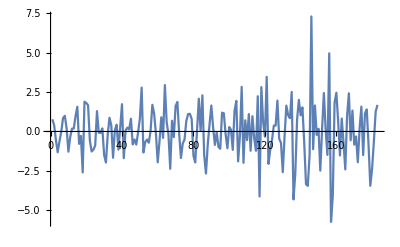

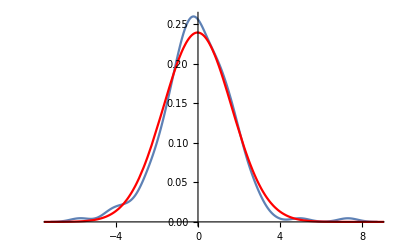

0.701235

```mathematica
residuals2 = Differences[residuals];
ListLinePlot[residuals2]
normDist = FindDistributionParameters[residuals2, NormalDistribution[nu,sigma]];
Show[SmoothHistogram[residuals2], Plot[PDF[NormalDistribution[normDist[[1, 2]],normDist[[2, 2]]],x], {x, -10, 10}, PlotStyle->Red]]
DistributionFitTest[residuals2, NormalDistribution[normDist[[1, 2]],normDist[[2, 2]]]]
```

Visually it seems we have succeeded in producing a more stationary series of residuals, that is still likely to originate from a normal distribution.
Let’s investigate correlation.

| Estimate | Standard Error | t-Statistic | P-Value
1 | -0.0262095 | 0.124236 | -0.210965 | 0.833153
x | -0.0414267 | 0.0746415 | -0.555009 | 0.579577

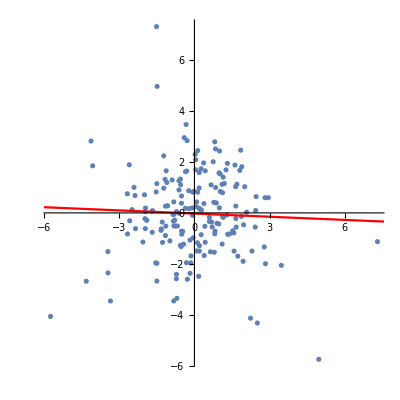

```mathematica
blurb2 = LinearModelFit[Partition[residuals2, 2, 1], {1, x}, x];
blurb2["ParameterTable"]
Show[ListPlot[Partition[residuals2, 2, 1], AspectRatio-> 1],Plot[blurb2[x],{x,-Length[residuals2],2*Length[residuals2]}, PlotStyle->Red]]
```

Now, the differences between two consecutive values seem to be randomly distributed and it is not possible to fit a straight line through the data, that has a slope differing from zero with statistical significance. What does the correlation plot look like?

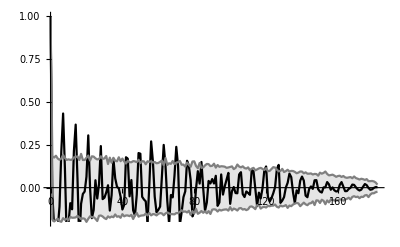

```mathematica
nVal2 = Length[residuals2] -1;
bands2={#[[5]],#[[-5]]}&/@(Sort/@Transpose[Table[CorrelationFunction[RandomSample[residuals2],{nVal2}],{800}]]);
ListLinePlot[Join[{Transpose[{Range[0,nVal2],CorrelationFunction[residuals2,{nVal2}]}],Transpose[{Range[0,nVal2],Transpose[bands2][[1]]}], 
Transpose[{Range[0,nVal2],Transpose[bands2][[2]]}]}],PlotStyle->{Black,Gray,Gray},Filling->{2->{3}}, PlotRange->{{0, nVal2},{-0.2, 1}}]
```

Even though there are still statistically significant periodic/seasonal correlations going on,  the values look less correlated.  A time series model from the Seasonal Autoregressive Integrated Moving Average (SARIMA) family should be able to address this issue. Let’s try to fit a model to the transformed data and generate a forecast for the next 30 days. Considering US case data, this should still well fall into the time period before the winter surge, and should thus neither correspond with a sharp increase nor decrease in COVID-19 case numbers.

TimeSeriesModel[…]

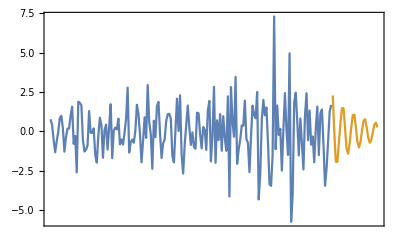

```mathematica
tsm = TimeSeriesModelFit[residuals2, "SARIMA"]
tsm["BestFit"];
eproc = Normal[tsm];
rawforecast=TimeSeriesForecast[eproc,TemporalData[residuals2],{30}];

DateListPlot[{TemporalData[residuals2],rawforecast["Path"]},Joined->True]
```

Now that we have a forecast, we need to reverse our alterations in order to gain forecasting information for our original data.
First, we reverse the differencing step to achieve forecasts for the residuals of our initial nonlinear model.

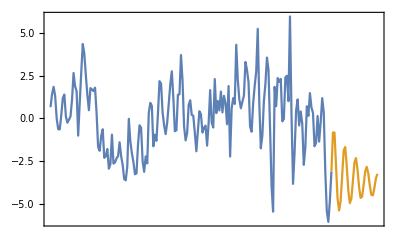

```mathematica
rawforecastTimes = Normal[TimeSeries[rawforecast]][[All, 1]];
rawforecastValues = Normal[TimeSeries[rawforecast]][[All, 2]];

toAccumulate = Prepend[rawforecastValues, residuals[[-1]]]; (* Making sure the forecast is adjacent to the residuals. *)
accforecast = Transpose[{(Append[rawforecastTimes, rawforecastTimes[[-1]]+1]),Accumulate[toAccumulate]}];

DateListPlot[{TemporalData[residuals],accforecast},Joined->True]
```

Next, we can add the forecast for our residuals to the original data.

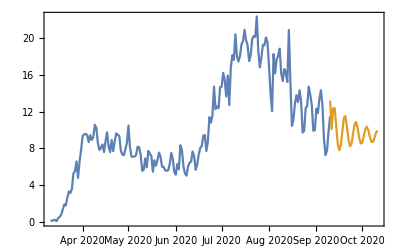

```mathematica
accforecastTS = TimeSeries[accforecast];
rawforecastValues = Normal[accforecastTS][[All, 2]];
(* Add last original data value for overlap.*)
forecastValues = Join[{Last[dataTS]}, rawforecastValues+ Last[dataTS]];

lastTimePoint=Last@dataTS["Times"] // DateObject;
Length[forecastValues]; (* We forecasted for 20 time points, had to accumulate the data to reverse transformations, and have one overlapping date. *)
forecast = TimeSeries[Transpose[{DateRange[lastTimePoint, lastTimePoint + ],forecastValues}]];
(*Plot forecast and data (overlapping on one date).*)
DateListPlot[{dataTS,forecast},Joined->True]
```

After undoing our data alterations, we can evaluate the forecast for our original data. It captures the fluctuating component well and, as initially stated, does not show a sharp increase or decrease in general trend, corresponding to the overall stationary case rate in the United States before the winter surge hit. However, this forecast does not perform well for longer periods of time:

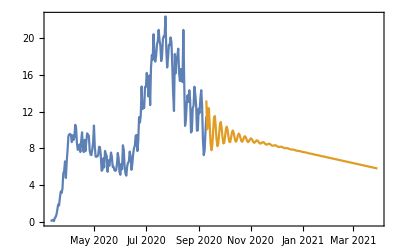

```mathematica
rawforecast=TimeSeriesForecast[eproc,TemporalData[residuals2],{200}];
rawforecastTimes = Normal[TimeSeries[rawforecast]][[All, 1]];
rawforecastValues = Normal[TimeSeries[rawforecast]][[All, 2]];
toAccumulate = Prepend[rawforecastValues, residuals[[-1]]];
accforecast = Transpose[{(Append[rawforecastTimes, rawforecastTimes[[-1]]+1]),Accumulate[toAccumulate]}];
accforecastTS = TimeSeries[accforecast];
rawforecastValues = Normal[accforecastTS][[All, 2]];
forecastValues = Join[{Last[dataTS]}, rawforecastValues+ Last[dataTS]];
lastTimePoint=Last@dataTS["Times"] // DateObject;
Length[forecastValues]; 
forecast = TimeSeries[Transpose[{DateRange[lastTimePoint, lastTimePoint + ],forecastValues}]];
DateListPlot[{dataTS,forecast},Joined->True]
```

This shows that the forecast we can calculate through time series analysis can not be used for a longer period of time. 
Leveraging Mathematica abilities, we can try to automate the process by fitting a time series model to our whole data and generating realisations from the captured process, with the intention of gaining a rough understanding of the trends in the data.

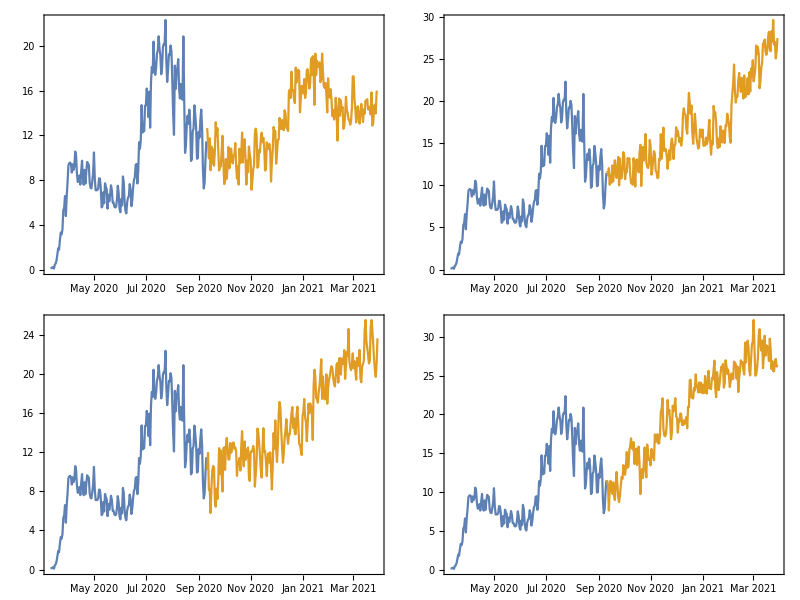

```mathematica
tsmAll = TimeSeriesModelFit[dataTS];
TableForm[Partition[Table[DateListPlot[{dataTS,RandomFunction[tsmAll,{200}]},PlotRange->All,ImageSize->Large],{4}],2]]
```

Yet even this step does not predict the severity of the winter surge. In sum, the additional summer 2020 surge in the US that differentiated from data concerning other G7 countries did not enable us to make trustworthy, long-term forecasts. This underlines the unpredictable nature of the pandemic, and forecasting its future course for a longer period of time has proven to be difficult. However, there are still valuable lessons that we can learn from the pandemic data that we have collected so far. By analyzing the patterns in the data, such as the course of the summer surge in the US, we can gain insights into the dynamics of the pandemic and use this information to inform our decisions about how to manage and respond to the pandemic in the short term.

### The Pandemic in the US During the Summer Months in 2020

Remembering our focus on US data, let's continue evaluating the chronological trends of confirmed cases for the G7 countries.  It is striking that only the US was exposed a summer surge, amounting to a second wave predating its equivalent in other countries, who had experienced a more relaxed pandemic in summer 2020.
Let's leverage the available data and have a look at state-level numbers. Is this rise in COVID-19 cases distributed equally among US states? First, we collect a list of all 48 mainland US states and their populations, including Alaska and Hawaii, since the external location and low population counts of these two might unnecessarily distort our analysis.

```mathematica
mainlandStates = EntityList[EntityClass["AdministrativeDivision","USStatesAllStates"]] // DeleteCases[#,  Entity["AdministrativeDivision",{"Hawaii","UnitedStates"}] |  Entity["AdministrativeDivision",{"Alaska","UnitedStates"}]]&;
mainlandStatesPop = Transpose[Dataset[<|"AdministrativeDivision" -> mainlandStates|>]][All,Append[#,"Population"->#AdministrativeDivision["Population"]]&];
GeoRegionValuePlot[mainlandStatesPop[All, {#AdministrativeDivision, #Population} &], ColorFunction->"Rainbow" ]
```

-Graphics-

In order to get a proxy for estimating the situation, we can use all ten states that have a population count of at least 10,000,000 inhabitants.

```mathematica
TakeLargestBy[mainlandStatesPop,"Population", 11] // #[SortBy["Population"]][Reverse]&
```

They account for more than half of the US population and enable less cluttered visualisations.

```mathematica
(tenMillionStatesPop[[All, "Population"]] //Total) / (mainlandStatesPop[[All, "Population"]] //Total) // N
```

0.545597

Let’s also create a list of these states and their populations.

```mathematica
tenMillionStates =  {Entity["AdministrativeDivision",{"California","UnitedStates"}],Entity["AdministrativeDivision",{"Florida","UnitedStates"}], Entity["AdministrativeDivision",{"Texas","UnitedStates"}], Entity["AdministrativeDivision",{"Georgia","UnitedStates"}], Entity["AdministrativeDivision",{"NewYork","UnitedStates"}], Entity["AdministrativeDivision",{"Illinois","UnitedStates"}], Entity["AdministrativeDivision",{"Pennsylvania","UnitedStates"}], Entity["AdministrativeDivision",{"Ohio","UnitedStates"}], Entity["AdministrativeDivision",{"NorthCarolina","UnitedStates"}], Entity["AdministrativeDivision",{"Michigan","UnitedStates"}]};
tenMillionStatesPop = Transpose[Dataset[<|"AdministrativeDivision" -> tenMillionStates|>]][All,Append[#,"Population"->#AdministrativeDivision["Population"]]&];
```

```mathematica
(* Set states and populations *)
states = tenMillionStates;
pop = tenMillionStatesPop;
```

Now we can collect pandemic data, which we will later restrict to these ten states.

```mathematica
pandemicByStates = ResourceData["Epidemic Data for Novel Coronavirus COVID-19", "USStates"][Select[#Country==Entity["Country", "UnitedStates"]&]][All, {"AdministrativeDivision", "ConfirmedCases", "Deaths"}];
```

In order to have a more closer look at the summer wave that is so unique to the US, we limit the data to the summer months.

```mathematica
pandemicByStates = MapAt[TimeSeriesWindow[#,  {{2020, 5, 1},{2020, 9, 30}}]&, pandemicByStates, {All, "ConfirmedCases"}];
```

Again, we smooth out the data to balance out daily fluctuations, which should help to gain a clearer picture of the situation, and transform the data from cumulative to showing incremental differences.

```mathematica
pandemicByStates = MapAt[MeanFilter[#,  604800]&, pandemicByStates , {All, "ConfirmedCases"}];
pandemicByStatesDif = MapAt[Differences, pandemicByStates,{All, "ConfirmedCases"}];
```

Let’s look at increase in case numbers.

```mathematica
tenMillionStatesDif = pandemicByStatesDif  // Select[MemberQ[states, #AdministrativeDivision]&]
```

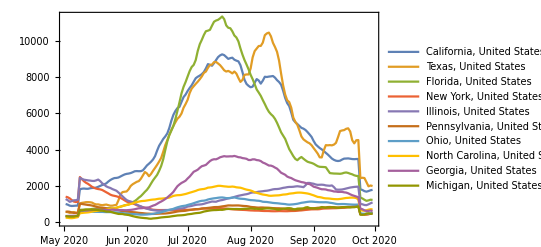

```mathematica
DateListPlot[(tenMillionStatesDif // #[All, "ConfirmedCases"]& //Normal), PlotLegends->(tenMillionStatesDif[All, "AdministrativeDivision"]// Normal), PlotRange->All]
```

Noticeably, three states seem to have experienced a remarkably strong increase in COVID-19 cases: California, Texas and Florida. Here, it is worth remembering that these three also make up the top three most populated states. Therefore, cases per 100,000 population (calculated analogously to the normalisation of counts per country) should give a less distorted picture.

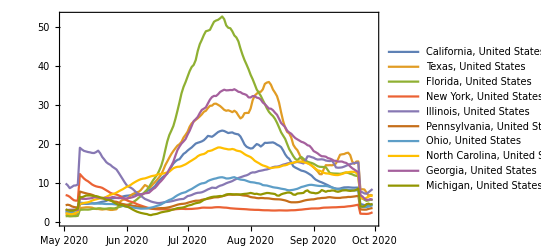

```mathematica
pandemicByStates = JoinAcross[mainlandStatesPop, pandemicByStates, Key["AdministrativeDivision"]];

norm[row_] := QuantityMagnitude[Divide[row["ConfirmedCases"],row["Population"]]]*100000
normedColumn = pandemicByStates[All,norm] // Normal;
pandemicByStates = Transpose[Append[Transpose[pandemicByStates],"Norm"->normedColumn]];
pandemicByStatesNormDif = MapAt[Differences, pandemicByStates,{All, "Norm"}];

tenMillionStatesDif = pandemicByStatesNormDif  // Select[MemberQ[states, #AdministrativeDivision]&] ;
DateListPlot[(tenMillionStatesDif // #[All, "Norm"]& //Normal), PlotLegends-> (tenMillionStatesDif[All, "AdministrativeDivision"]// Normal), PlotRange->All]
```

Despite now accounting for differences in population sizes, there appear to be notable disparities in the data of COVID-19 case increases across the ten most populous US states. Specifically, states located in the “sun belt” region, such as Florida, Texas, and Georgia, seem to have exhibited stronger increases in case numbers and experienced a particularly significant surge during the summer months. The visualised differences suggest that regional factors may be playing a significant role in the transmission and spread of the virus. These could comprise demographics, public health policies, but also climate factors. Considering that the virus spreads primarily via contact [3], the increased spread (visualised through the observed higher spike in COVID-19 cases) in warmer southern states during summer months may be expected. The summer heat may have driven people indoors to seek refuge in air-conditioned environments, leading to more indoor gatherings and less physical distancing. This behavior may have increased the risk of transmission of the virus in those states, leading to the higher number of confirmed cases. 
Potentially, using temperature data could help us confirm this hypothesis. Since states located in the south tend to be warmer in the summer, we could use latitude as a stable proxy to eliminate potential year-to-year variation in temperature.

#### Using Latitude to Estimate Summer Surge Susceptibility

Capital cities might not always provide an accurate assessment of the geographic location of an administrative entity. Let’s use Wolfram data to directly infer the geographic position of a state.

```mathematica
centroids = Transpose[Dataset[<|"AdministrativeDivision" -> mainlandStates|>]][All,Append[#,"Position"->#AdministrativeDivision["Position"]]&]
GeoListPlot[((centroids// Select[MemberQ[states, #AdministrativeDivision]&] )[All, "Position"]// Normal)]
```

-Graphics-

This helped condense the complexity of a proxy for average warmth into one single value, the geographic position. Let’s get rid of redundant longitudinal data.

```mathematica
latitudes = MapAt[Latitude,centroids[All, {"AdministrativeDivision", "Position"}], {All, "Position"}];
```

We can further simplify the latitudinal position into a relative value between zero and one, with zero corresponding to the latitude of the southernmost US state, and one representing the latitude of the northernmost US state.

```mathematica
latMin = Min[Latitude /@ EntityValue[EntityClass["AdministrativeDivision","USStatesAllStates"], "Position"]];
latMax = Max[Latitude /@ EntityValue[EntityClass["AdministrativeDivision","USStatesAllStates"], "Position"]];
normLatitudes = MapAt[Rescale[#, {latMin, latMax}]&,latitudes[All, {"AdministrativeDivision", "Position"}], {All, "Position"}]
allData =JoinAcross[pandemicByStatesNormDif, normLatitudes, "AdministrativeDivision"];
```

Utilizing the visual representation of the normalised case increments, we can infer that the peak of the second wave of COVID-19 in the United States occurred around the beginning to mid July 2020. This time period most distinctively distinguishes the states, presenting significant implications for our inquiry. We can now proceed to identify which states faced the most severe outbreak and whether there is any correlation with the longitudinal position. The exploration of such information is crucial in the formulation of protective measures that can be instituted to reduce the impact of the virus on those states most at risk.
First, let’s extract the normalised case count on July 10, 2020, for each state.

```mathematica
allData = allData[All,Append[#,"Value"->#Norm["July 10, 2020"]]&];
```

Next, we can group the July 10 value with the latitudinal position corresponding to the same state, and plot these data for all states.

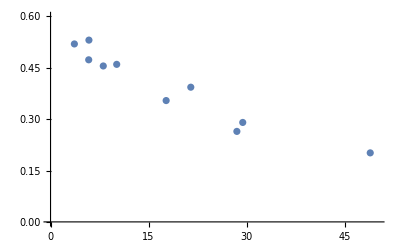

```mathematica
normCasesByLatitude = Transpose[{Normal[(allData// Select[MemberQ[states, #AdministrativeDivision]&])[[All, "Value"]]],Normal[(allData// Select[MemberQ[states, #AdministrativeDivision]&])[[All, "Position"]]]}];
ListPlot[normCasesByLatitude, PlotRange->{xRange[[2;;]], yRange[[2;;]]}]
```

This looks like we might be able to fit a straight line that decently models the data. Let’s fit a simple linear model.

FittedModel[0.529197-0.00751301 x]

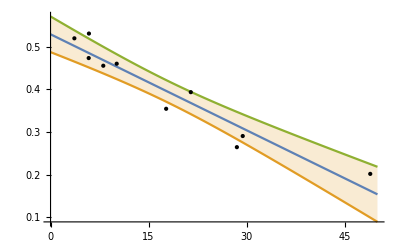

```mathematica
lm = LinearModelFit[normCasesByLatitude, {1, x}, x]
xRange = {x, 0, 50};
yRange = {x, 0, 0.6};
With[{expr= Join[{lm[x]},lm["MeanPredictionBands"]]},Plot[expr,xRange,Epilog-> {Point[normCasesByLatitude]},Filling-> {2-> {3}}]]
```

Visually, this model seems to fit the data quite nicely. The adjusted R-Squared value being quite close to one supports this impression. This suggests that more than 90% of the variation in the response variable (severity of COVID-19 case numbers in summer 2020) can be explained by the predictor variable (state latitude), while taking into account the number of predictor variables in the model.

```mathematica
lm["AdjustedRSquared"]
```

0.905493

The drawback of this simple model is that for theoretical states that have a more northern location (say, Alaska), this equation would predict negative case counts, contradicting common sense. In order to investigate whether it might be more appropriate to use a more complex model here, we can add a component to our model and compare the adjusted R-Squared values.

FittedModel[0.566742-0.0124815 x+0.000101433 x^2]

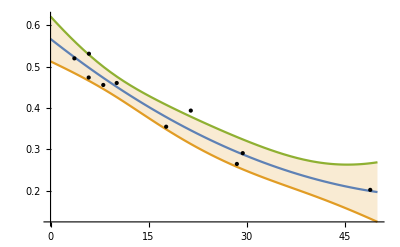

{0.905493,0.935165}

```mathematica
lmAlt = LinearModelFit[normCasesByLatitude, {1, x, x^2}, x]
With[{expr= Join[{lmAlt[x]},lmAlt["MeanPredictionBands"]]},Plot[expr,xRange,Epilog-> {Point[normCasesByLatitude]},Filling-> {2-> {3}}]]
{lm["AdjustedRSquared"], lmAlt["AdjustedRSquared"]}
```

The higher adjusted R-squared value for the alternative model suggests a better fit to the data, as the model explains a greater proportion of variance in the response variable. However, we should also consider the ANOVA tables to check the p-value of the additional component. The statistical significance of a predictor variable indicates whether it is likely to be a true contributor to the response variable or if the observed relationship could have occurred by chance.

```mathematica
{lm["ANOVATable"],lmAlt["ANOVATable"]}
```

{ | DF | SS | MS | F-Statistic | P-Value
x | 1 | 0.105466 | 0.105466 | 87.2307 | 0.0000141011
Error | 8 | 0.00967239 | 0.00120905 |  | 
Total | 9 | 0.115139 |  |  | , | DF | SS | MS | F-Statistic | P-Value
x | 1 | 0.105466 | 0.105466 | 127.153 | 9.64238×10^-6
x^2 | 1 | 0.00386629 | 0.00386629 | 4.66132 | 0.067707
Error | 7 | 0.0058061 | 0.000829443 |  | 
Total | 9 | 0.115139 |  |  | }

The p-value for the additional x.b2 component is not small enough for the component to contribute significantly. This suggests that the concerned predictor variable may not be a useful addition to the model, even if it increases the adjusted R-squared value. The parameter tables for the models shed further light onto the situation. The absolute contribution of the x.b2 component is nearly zero.

```mathematica
{lm["ParameterTable"],lmAlt["ParameterTable"]}
```

{ | Estimate | Standard Error | t-Statistic | P-Value
1 | 0.529197 | 0.0181467 | 29.1621 | 2.07026×10^-9
x | -0.00751301 | 0.000804414 | -9.33974 | 0.0000141011, | Estimate | Standard Error | t-Statistic | P-Value
1 | 0.566742 | 0.0229852 | 24.6568 | 4.59987×10^-8
x | -0.0124815 | 0.0023958 | -5.20975 | 0.00123966
x^2 | 0.000101433 | 0.0000469814 | 2.15901 | 0.067707}

Moreover, while the alternative model does not bear the risk of predicting negative counts, including an additional parameter could have potentially risked overfitting of the model due to the small dataset size. To conclude, in this case, we would prefer the simpler model and only use the pure latitudes for predicting the severity of COVID-19 case numbers in summer 2020, since this predictor appears to be highly significant in both models.

Since we reduced all case data to one value per state, the resulting dataset of ten data points is very small. What happens if, now, we do include all states here?

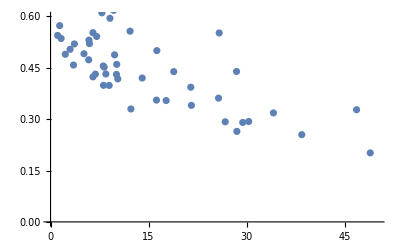

```mathematica
normCasesByLatitude1 = Transpose[{Normal[allData[[All, "Value"]]],Normal[allData[[All, "Position"]]]}];
ListPlot[normCasesByLatitude1, PlotRange->{xRange[[2;;]], yRange[[2;;]]}]
```

Let’s fit both types of models once more.

FittedModel[0.536738-0.00646474 x]

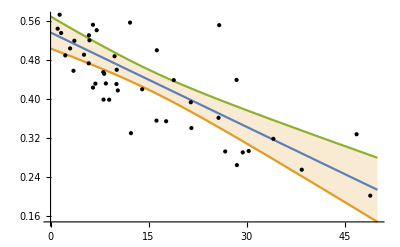

FittedModel[0.546863-0.00802384 x+0.0000360138 x^2]

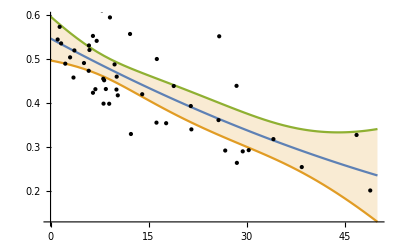

{0.531777,0.524522}

```mathematica
lm1 = LinearModelFit[normCasesByLatitude1, {1, x}, x]
xRange = {x, 0, 50};
yRange = {x, 0, 0.6};
With[{expr= Join[{lm1[x]},lm1["MeanPredictionBands"]]},Plot[expr,xRange,Epilog-> {Point[normCasesByLatitude1]},Filling-> {2-> {3}}]]
lmAlt1 = LinearModelFit[normCasesByLatitude1, {1, x, x^2}, x]
With[{expr= Join[{lmAlt1[x]},lmAlt1["MeanPredictionBands"]]},Plot[expr,xRange,Epilog-> {Point[normCasesByLatitude1]},Filling-> {2-> {3}}]]
{lm1["AdjustedRSquared"], lmAlt1["AdjustedRSquared"]}
```

Here, the alternative model with a higher adjusted R-squared value implies a worse fit to the data since it explains a smaller portion of the variance in the response variable.

```mathematica
{lm1["ANOVATable"],lmAlt1["ANOVATable"]}
```

{ | DF | SS | MS | F-Statistic | P-Value
x | 1 | 0.274612 | 0.274612 | 54.3794 | 2.5093×10^-9
Error | 46 | 0.232297 | 0.00504993 |  | 
Total | 47 | 0.506909 |  |  | , | DF | SS | MS | F-Statistic | P-Value
x | 1 | 0.274612 | 0.274612 | 53.5497 | 3.45103×10^-9
x^2 | 1 | 0.00152891 | 0.00152891 | 0.298138 | 0.587749
Error | 45 | 0.230768 | 0.00512818 |  | 
Total | 47 | 0.506909 |  |  | }

The ANOVA table confirms that the additional x.b2 component does not appear to be a true contributor to the response variable. Overall, the model equations are closely similar to their respective equivalent for the model for the 10 most populated states. However, a notably greater portion of the variance remains unexplained, most likely due to the larger dataset at use, indicating a worse fit. Despite this, the model based on the 10 most populated states already covers over 50% of the US population, which allows for overall inferences and recommendations that are applicable to a majority of the population.
Using latitude as a proxy for temperature, we observed that southern states, including Florida, Texas, and Georgia, showed a surge in COVID-19 cases during summer months. This indicates that regional factors, including climate, may have a significant role in the virus’s transmission and spread. Due to the virus spreading primarily through contact, the warmer weather in the south drove people indoors, resulting in more indoor gatherings and less physical distancing, thus increasing the risk of transmission. However, these states located along the sun belt were in fact among the first to open up after the primary COVID-19 wave [4]. Our model shows that for the majority of the US population, the intensity of the summer surge can indeed be predicted confidently from state latitude, highlighting the need to focus hospital resources and COVID protection measures on these states, especially during future pandemic summers. This would allow for more effective allocation of resources and implementation of preventive measures, ultimately leading to better control of the spread of the virus and potentially saving lives.

In conclusion, while forecasting the pandemic is challenging, exploring pandemic data can still provide valuable insights. Our analysis of the US pandemic data pertaining to summer 2020 showed that state latitude is a significant predictor of pandemic intensity, providing useful information for future pandemic preparedness. The findings highlight the importance of continued data analysis and preparation for future pandemics, as well as the need for targeted resources and measures to protect the population. By leveraging data and technology, we can continue to learn and improve our response to global challenges such as the COVID-19 pandemic.

References:
[1]  Wolfram Research. “Epidemic Data for Novel Coronavirus COVID-19” from the Wolfram Data Repository (2022)  https://doi.org/10.24097/wolfram.04123.data 
[2] Centers for Disease Control and Prevention. “COVID-19 timeline” (2023). Retrieved April 26, 2023, from https://www.cdc.gov/museum/timeline/covid19.html
[3] NHS. “How to avoid catching and spreading coronavirus (COVID-19)” (2021). Retrieved April 26, 2023, from https://www.nhs.uk/conditions/covid-19/how-to-avoid-catching-and-spreading-covid-19/
[4] The New York Times. “Coronavirus Cases and Reopening Trends by State (2020, July 9)”. Retrieved April 27, 2023, from https://www.nytimes.com/interactive/2020/07/09/us/coronavirus-cases-reopening-trends.html